# Homework 1

#### 1)

```mathematica
f[x_, y_] := ((x+y)^2 - (2*x*y) - y^2 / x^2);
```

```mathematica
y=10^3
```

1000

```mathematica
For[i=1, i≤8, ++i, 
Print[f[10.0^-i, y]];
];
```

-9.9×10^7

-9.999×10^9

-9.99999×10^11

-1.×10^14

-1.×10^16

-1.×10^18

-1.×10^20

-1.×10^22

```mathematica
fffferrorlist= {};
```

```mathematica
For[i=1,i≤8, ++i,
e= Abs[f[10.0^-i,y] - 1];
Print[e];
AppendTo[fffferrorlist,e]
];
```

9.9×10^7

9.999×10^9

9.99999×10^11

1.×10^14

1.×10^16

1.×10^18

1.×10^20

1.×10^22

```mathematica
fffferrorlist
```

{9.9×10^7,9.999×10^9,9.99999×10^11,1.×10^14,1.×10^16,1.×10^18,1.×10^20,1.×10^22}

```mathematica
ListPlot[fffferrorlist]
```

-Graphics-

### 2)

```mathematica
g[x_, y_] := ((x+y)^2)/ x^2 - ((2*x*y)/ x^2) - y^2/x^2; 
gerrorlist = {};
y=10^3;
```

```mathematica
For[i=1, i≤8,++i,
Print[g[10^-i, y]];
];
```

1

1

1

«5 more identical outputs»

```mathematica
For[i=1,i≤8,++i,
err= Abs[1- g[10^-i, y]];
AppendTo[gerrorlist,err];
];
gerrorlist
```

```mathematica
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

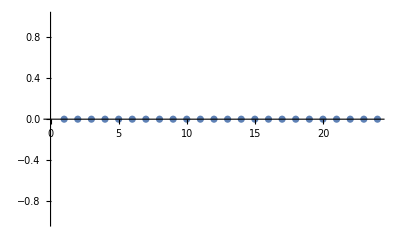

```mathematica
ListPlot[gerrorlist]
```

functions g and f are identical but Mathematica must be doing the order of operations differently, producing different results.

### 3)

```mathematica
For[i=1,i≤8,++i,
Print[f[10^-i, y]];
];
```

-9899999999/100

-99989999999999/10000

-999998999999999999/1000000

-9999999899999999999999/100000000

-99999999989999999999999999/10000000000

-999999999998999999999999999999/1000000000000

-9999999999999899999999999999999999/100000000000000

-99999999999999989999999999999999999999/10000000000000000

```mathematica
herrorlist={};
For[i=1,i≤8,++i,
erro= Abs[1-f[10^-i,y]];
AppendTo[herrorlist,erro];
];
```

```mathematica
herrorlist
```

{9900000099/100,99990000009999/10000,999999000000999999/1000000,9999999900000099999999/100000000,99999999990000009999999999/10000000000,999999999999000000999999999999/1000000000000,9999999999999900000099999999999999/100000000000000,99999999999999990000009999999999999999/10000000000000000}

```mathematica
ListPlot[herrorlist]
```

-Graphics-

The results are different because converting the value from a double value to an integer value tells Mathematica that you care about significant figures for question 1 but not for question 3.

## Collatz Conjecture

```mathematica
s=10;
count= 0;
values={};
```

```mathematica
While[s≠1,
If[EvenQ[s]==True,
s= s/2,
s = (3*s)+1;];
count=count+1;
AppendTo[valuess,s]
];
Print[count];
```

6

#### Answer Below:

```mathematica
For[i=1,i≤2000,++i,
n=i;
counter=0;
While[n≠1,
If[EvenQ[n]==True,
n=n/2,
n=(n*3)+1;];
counter=counter+1;];
AppendTo[values, counter];];
```

```mathematica
values
```

{0,1,7,2,5,8,16,3,19,6,14,9,9,17,17,4,12,20,20,7,7,15,15,10,23,10,111,18,18,18,106,5,26,13,13,21,21,21,34,8,109,8,29,16,16,16,104,11,24,24,24,11,11,112,112,19,32,19,32,19,19,107,107,6,27,27,27,14,14,14,102,22,115,22,14,22,22,35,35,9,22,110,110,9,9,30,30,17,30,17,92,17,17,105,105,12,118,25,25,25,25,25,87,12,38,12,100,113,113,113,69,20,12,33,33,20,20,33,33,20,95,20,46,108,108,108,46,7,121,28,28,28,28,28,41,15,90,15,41,15,15,103,103,23,116,116,116,23,23,15,15,23,36,23,85,36,36,36,54,10,98,23,23,111,111,111,67,10,49,10,124,31,31,31,80,18,31,31,31,18,18,93,93,18,44,18,44,106,106,106,44,13,119,119,119,26,26,26,119,26,18,26,39,26,26,88,88,13,39,39,39,13,13,101,101,114,26,114,52,114,114,70,70,21,52,13,13,34,34,34,127,21,83,21,127,34,34,34,52,21,21,96,96,21,21,47,47,109,47,109,65,109,109,47,47,8,122,122,122,29,29,29,78,29,122,29,21,29,29,42,42,16,29,91,91,16,16,42,42,16,42,16,60,104,104,104,42,24,29,117,117,117,117,117,55,24,73,24,117,16,16,16,42,24,37,37,37,24,24,86,86,37,130,37,37,37,37,55,55,11,24,99,99,24,24,24,143,112,50,112,24,112,112,68,68,11,112,50,50,11,11,125,125,32,125,32,125,32,32,81,81,19,125,32,32,32,32,32,50,19,45,19,45,94,94,94,45,19,19,45,45,19,19,45,45,107,63,107,58,107,107,45,45,14,32,120,120,120,120,120,120,27,58,27,76,27,27,120,120,27,19,19,19,27,27,40,40,27,40,27,133,89,89,89,133,14,133,40,40,40,40,40,32,14,58,14,53,102,102,102,40,115,27,27,27,115,115,53,53,115,27,115,53,71,71,71,97,22,115,53,53,14,14,14,40,35,128,35,128,35,35,128,128,22,35,84,84,22,22,128,128,35,35,35,27,35,35,53,53,22,48,22,22,97,97,97,141,22,48,22,141,48,48,48,97,110,22,48,48,110,110,66,66,110,61,110,35,48,48,48,61,9,35,123,123,123,123,123,61,30,123,30,123,30,30,79,79,30,30,123,123,30,30,22,22,30,22,30,48,43,43,43,136,17,43,30,30,92,92,92,43,17,136,17,30,43,43,43,87,17,43,43,43,17,17,61,61,105,56,105,30,105,105,43,43,25,30,30,30,118,118,118,30,118,56,118,118,118,118,56,56,25,74,74,74,25,25,118,118,17,56,17,69,17,17,43,43,25,131,38,38,38,38,38,69,25,131,25,131,87,87,87,131,38,25,131,131,38,38,38,38,38,30,38,30,56,56,56,131,12,51,25,25,100,100,100,38,25,144,25,100,25,25,144,144,113,51,51,51,113,113,25,25,113,51,113,144,69,69,69,95,12,64,113,113,51,51,51,64,12,64,12,38,126,126,126,38,33,126,126,126,33,33,126,126,33,126,33,64,82,82,82,170,20,33,126,126,33,33,33,64,33,25,33,25,33,33,51,51,20,46,46,46,20,20,46,46,95,33,95,139,95,95,46,46,20,139,20,20,46,46,46,95,20,90,20,46,46,46,46,139,108,20,64,64,108,108,59,59,108,33,108,152,46,46,46,59,15,33,33,33,121,121,121,152,121,33,121,59,121,121,121,121,28,121,59,59,28,28,77,77,28,77,28,103,121,121,121,72,28,59,20,20,20,20,20,72,28,46,28,134,41,41,41,134,28,41,41,41,28,28,134,134,90,134,90,41,90,90,134,134,15,28,134,134,41,41,41,85,41,41,41,41,41,41,33,33,15,59,59,59,15,15,54,54,103,28,103,147,103,103,41,41,116,147,28,28,28,28,28,178,116,147,116,28,54,54,54,147,116,116,28,28,116,116,54,54,72,147,72,46,72,72,98,98,23,67,116,116,54,54,54,116,15,67,15,54,15,15,41,41,36,129,129,129,36,36,129,129,36,129,36,67,129,129,129,116,23,129,36,36,85,85,85,129,23,173,23,85,129,129,129,36,36,36,36,36,36,36,28,28,36,28,36,28,54,54,54,129,23,49,49,49,23,23,23,142,98,49,98,36,98,98,142,142,23,98,49,49,23,23,142,142,49,23,49,36,49,49,98,98,111,93,23,23,49,49,49,49,111,142,111,41,67,67,67,93,111,111,62,62,111,111,36,36,49,155,49,62,49,49,62,62,10,36,36,36,124,124,124,36,124,155,124,124,124,124,62,62,31,124,124,124,31,31,124,124,31,62,31,93,80,80,80,168,31,80,31,31,124,124,124,75,31,75,31,62,23,23,23,168,31,23,23,23,31,31,49,49,44,137,44,137,44,44,137,137,18,44,44,44,31,31,31,75,93,137,93,31,93,93,44,44,18,93,137,137,18,18,31,31,44,137,44,93,44,44,88,88,18,44,44,44,44,44,44,137,18,36,18,36,62,62,62,62,106,18,57,57,106,106,31,31,106,150,106,57,44,44,44,57,26,150,31,31,31,31,31,57,119,181,119,150,119,119,31,31,119,57,57,57,119,119,119,119,119,31,119,57,57,57,57,88,26,150,75,75,75,75,75,49,26,101,26,119,119,119,119,70,18,57,57,57,18,18,70,70,18,57,18,70,44,44,44,163,26,132,132,132,39,39,39,132,39,132,39,132,39,39,70,70,26,132,132,132,26,26,132,132,88,39,88,70,88,88,132,132,39,176,26,26,132,132,132,88,39,39,39,83,39,39,39,176,39,39,31,31,39,39,31,31,57,31,57,83,57,57,132,132,13,52,52,52,26,26,26,145,101,145,101,52,101,101,39,39,26,101,145,145,26,26,101,101,26,52,26,176,145,145,145,101,114,26,52,52,52,52,52,145,114,101,114,52,26,26,26,52,114,52,52,52,114,114,145,145,70,44,70,26,70,70,96,96,13,114,65,65,114,114,114,158,52,39,52,114,52,52,65,65,13,52,65,65,13,13,39,39,127,39,127,114,127,127,39,39,34,158,127,127,127,127,127,96,34,65,34,65,127,127,127,114,34,34,127,127,34,34,65,65,83,96,83,127,83,83,171,171,21,83,34,34,127,127,127,34,34,78,34,127,34,34,65,65,34,26,26,26,34,34,26,26,34,26,34,78,52,52,52,127,21,140,47,47,47,47,47,52,21,140,21,140,47,47,47,140,96,34,34,34,96,96,140,140,96,34,96,140,47,47,47,171,21,96,140,140,21,21,21,96,47,34,47,140,47,47,96,96,21,47,91,91,21,21,47,47,47,47,47,47,47,47,140,140,109,39,21,21,65,65,65,91,109,65,109,140,60,60,60,153,109,109,34,34,109,109,153,153,47,60,47,60,47,47,60,60,16,153,34,34,34,34,34,109,122,60,122,34,122,122,153,153,122,122,34,34,122,122,60,60,122,60,122,153,122,122,122,60,29,34,122,122,60,60,60,60,29,91,29,122,78,78,78,166,29,78,78,78,29,29,104,104,122,122,122,73,122,122,73,73,29,60,60,60,21,21,21,166,21,73,21,21,21,21,73,73,29,47,47,47,29,29,135,135,42,135,42,73,42,42,135,135,29,135,42,42,42,42,42,104,29,73,29,73,135,135,135,135,91,29,135,135,91,91,42,42,91,73,91,42,135,135,135,73,16,179,29,29,135,135,135,42,42,91,42,135,42,42,86,86,42,42,42,42,42,42,42,42,42,34,42,135,34,34,34,179,16,34,60,60,60,60,60,60,16,135,16,148,55,55,55,148,104,29,29,29,104,104,148,148,104,55,104,55,42,42,42,55,117,104,148,148,29,29,29,104,29,104,29,55,29,29,179,179,117,148,148,148,117,117,29,29,55,55,55,42,55,55,148,148,117,104,117,117,29,29,29,148,117,55,117,55,55,55,55,86,73,117,148,148,73,73,47,47,73,29,73,47,99,99,99,99,24,117,68,68,117,117,117,68,55,161,55,42,55,55,117,117,16,55,68,68,16,16,55,55,16,68,16,161,42,42,42,161,37,42,130,130,130,130,130,68,37,42,37,130,130,130,130,161,37,130,130,130,37,37,68,68,130,68,130,130,130,130,117,117,24,37,130,130,37,37,37,68,86,68,86,37,86,86,130,130,24,86,174,174,24,24,86,86,130,37,130,86,130,130,37,37,37,81,37,37,37,37,37,174,37,68,37,68,29,29,29,130,37,37,29,29,37,37,29,29,55,81,55,174,55,55,130,130,24,143,50,50,50,50,50,50,24,55,24,143,24,24,143,143,99,50,50,50,99,99,37,37,99,37,99,81,143,143,143,174,24,37,99,99,50,50,50,81,24,174,24,81,143,143,143,99,50,24,24,24,50,50,37,37,50,143,50,143,99,99,99,50,112,50,94,94,24,24,24,50,50,50,50,50,50,50,50,50,112}

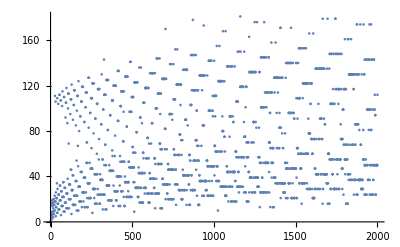

```mathematica
ListPlot[values]
```

### Note: Questions 1-3 have weird variable assignment name because I have made mistakes and did not know how to clear the list values until I figured out how to do it when doing the Collatz Conjecture assignment.

#### Newton’s Method

```mathematica
(* Subscript[x, n+1]= Subscript[x, n] - f(Subscript[x, n])/f'(Subscript[x, n]) *)
```

#### 1)

```mathematica
f[x_]:= x^2;
```

```mathematica
Guess=0.5;
```

```mathematica
While[Abs[f[Guess]]>10^-5,
Guess=Guess-f[Guess]/f'[Guess]];
Print[{N[Guess],N[f[Guess]]}];
```

{0.00195313,3.8147×10^-6}

#### 2)

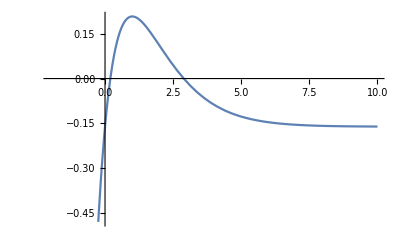

```mathematica
Plot[(x*E^-x)-0.16064,{x,-2,10}]
```

```mathematica
FindRoot[x E^-x-0.16064,{x,3}]
```

{x→2.88976}

```mathematica
g[x_] := (x*E^-x)-0.16064;
```

```mathematica
Guess=3;
```

#### 2b) (Ignore For Loop)

```mathematica
For[i=1,i≤10,i++,
Guess=Guess-g[Guess]/g'[Guess];]
Print[{N[Guess,10],N[g[Guess],10]}]
```

{2.88976,-2.77556×10^-17}

```mathematica
counter=0;
```

```mathematica
While[Abs[g[Guess]]>10^-5 && counter≤100,
Guess=Guess-g[Guess]/g'[Guess];
counter++;]
Print[{N[Guess],N[f[Guess]]}];
```

{2.88976,2.27381×10^-7}

```mathematica
counter
```

2

```mathematica
While[Abs[g[Guess]]>10^-2 && counter≤100,
Guess=Guess-g[Guess]/g'[Guess];
counter++;]
Print[{N[Guess],N[f[Guess]]}];
```

{2.88673,0.000319031}

```mathematica
counter
```

1

```mathematica
(*relative absolute error*)
error= Abs[2.88976-2.88673]/Abs[2.99076]
```

```mathematica
0.001013120410865421
```

Just over 0.1% error.

#### Midpoint Method

```mathematica
h[x_]:=x^3;
```

```mathematica
c=2;
```

```mathematica
a=-1;
```

```mathematica
b=1;
```

```mathematica
While[Abs[h[c]]> 10^-5 ,
If[f[c] > 0,
b = c,
a=c];
c=(a+b)/2;];
```

```mathematica
Print[{c,h[c]}]
```

{0,0}

```mathematica
Plot[(x*E^-x)-0.16064,{x,-2,10}]
```

-Graphics-

```mathematica
FindRoot[x E^-x-0.16064,{x,3}]
```

{x→2.88976}

```mathematica
m[x_]:=(x*E^-x)-0.16064;
```

```mathematica
count=0;
```

```mathematica
j=2;
```

```mathematica
k=4;
```

```mathematica
range=2.5;
```

```mathematica
While[Abs[m[range]> 10^{-5}] && count≤100,
If[m[range]>0,
k= range,
j=range];
range=(j+k)/2;
count++];
Print[{range,m[range]}]
```

{2.5,0.0445725}